# Data Processing of Amira Material Statistics Output

## Working Directories and global variable definitions :

```mathematica
myExportDirectory=FileNameJoin[{$HomeDirectory,"Documents","BIOLOGIE","DiplomaThesis","DATA_ANALYSIS","cleaned_MaterialStatistics_CSV_Files"}]
```

/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/DATA_ANALYSIS/cleaned_MaterialStatistics_CSV_Files

```mathematica
myDirectory = FileNameJoin[{$HomeDirectory,"Documents","BIOLOGIE","DiplomaThesis","MaterialStatistics","CSV"}]
```

/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV

```mathematica
mySegmentsList={"dactylus","propodus","carpus","merus","ischium","basis"};
myNameingList={"hatch","large_mal","med_mal","large_fem","med_fem","sm01_fem","sm01_mal","sm_fem","sm_mal"};

(*"or" list for regex.b4s, already useable because it is a string:*)
myNameingOrList="("<>StringReplace[ToString[myNameingList],{","->"|",RegularExpression["{|}"]->""," "->""}]<>")";
mySegmentsOrList="("<>StringReplace[ToString[mySegmentsList],{","->"|",RegularExpression["{|}"]->""," "->""}]<>")";
```

## Filtering of unprocessed files and global variable definitions:

```mathematica
myFilepathsUnprocessedGnath1=FileNames[RegularExpression[".*"<>myNameingOrList]~~RegularExpression[".*?_gnath1.*?\\.csv$"],{myDirectory},Infinity]
```

{/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_hatch_4x_unst_detail-gnathopods_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_large_mal_4x_unst_detail-gnathopods_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_med_mal_4x_unst_detail-gnathopods_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_fem_4x_unst_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_mal_4x_unst_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_large_fem_4x_unst_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_med_fem_4x_unst_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_fem_4x_unst_ber_gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_mal_4x_unst_detail-gnathopods_ber_gnath1r-filtered.csv}

```mathematica
myFilepathsUnprocessedGnath2=FileNames[RegularExpression[".*"<>myNameingOrList]~~RegularExpression[".*?_gnath2.*?\\.csv$"],{myDirectory},Infinity]
```

{/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_hatch_4x_unst_detail-gnathopods_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_large_mal_4x_unst_detail-gnathopods_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_med_mal_4x_unst_detail-gnathopods_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_fem_4x_unst_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_mal_4x_unst_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_large_fem_4x_unst_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_med_fem_4x_unst_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_fem_4x_unst_ber_gnath2r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_mal_4x_unst_detail-gnathopods_ber_gnath2r.csv}

```mathematica
myFilepathsUnprocessedVol1=FileNames[RegularExpression[".*"<>myNameingOrList]~~RegularExpression[".*?vol1gnath1.*?\\.csv$"],{myDirectory},Infinity]
```

{/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_hatch_4x_unst_detail-gnathopods_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_large_mal_4x_unst_detail-gnathopods_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_med_mal_4x_unst_detail-gnathopods_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_fem_4x_unst_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_mal_4x_unst_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_large_fem_4x_unst_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_med_fem_4x_unst_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_fem_4x_unst_ber_vol1gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_mal_4x_unst_detail-gnathopods_ber_vol1gnath1r-filtered.csv}

```mathematica
myFilepathsUnprocessedVol2=FileNames[RegularExpression[".*"<>myNameingOrList]~~RegularExpression[".*?vol2gnath1.*?\\.csv$"],{myDirectory},Infinity]
```

{/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_hatch_4x_unst_detail-gnathopods_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_large_mal_4x_unst_detail-gnathopods_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pair_med_mal_4x_unst_detail-gnathopods_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_fem_4x_unst_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp02_sm_mal_4x_unst_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_large_fem_4x_unst_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_med_fem_4x_unst_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_fem_4x_unst_ber_vol2gnath1r.csv,/Users/brosensteiner/Documents/BIOLOGIE/DiplomaThesis/MaterialStatistics/CSV/lab_pp_sm01_mal_4x_unst_detail-gnathopods_ber_vol2gnath1r-filtered.csv}

```mathematica
(*counting files and saving in specified variable for reuse*)
myFileCountGnath1=Length[myFilepathsUnprocessedGnath1];
myFileCountGnath2=Length[myFilepathsUnprocessedGnath2];
myFileCountVol1=Length[myFilepathsUnprocessedVol1];
```

## “CleanUp” Loop (saves new cleaned up files at myExportDirectory):

```mathematica
myRemovedItemsRegEx=RegularExpression[".*?(Table1|all|Exterior|Inside|rest).*?\n"];(*lines which i will remove in every table*)
```

```mathematica
(*Gnathopod 1*)
For[i=1,i<=myFileCountGnath1,i++,
myTempFile=StringReplace[
Import[myFilepathsUnprocessedGnath1[[i]],"String"],{";"->",",myRemovedItemsRegEx->""}];
Export[StringJoin[myExportDirectory,"/",FileBaseName[myFilepathsUnprocessedGnath1[[i]]],".txt"],myTempFile,"String"];
]
```

```mathematica
(*Gnathopod 2*)
For[i=1,i<=myFileCountGnath2,i++,
myTempFile=StringReplace[
Import[myFilepathsUnprocessedGnath2[[i]],"String"],{";"->",",myRemovedItemsRegEx->""}];
Export[StringJoin[myExportDirectory,"/",FileBaseName[myFilepathsUnprocessedGnath2[[i]]],".txt"],myTempFile,"String"];
]
```

```mathematica
(*Gnathopod Volumes, with additional combination of the vol1 and vol2 files*)

For[i=1,i≤myFileCountVol1,i++,

myTempFile1=StringReplace[Import[myFilepathsUnprocessedVol1[[i]],"String"],{";"->",",myRemovedItemsRegEx->""}];

myFilepathsUnprocessedVol1Temp=myFilepathsUnprocessedVol1[[i]];
myVol2PathTemp=StringReplace[myFilepathsUnprocessedVol1Temp,"vol1"->"vol2"];
myTempFile2=StringReplace[Import[myVol2PathTemp,"String"],{";"->",",myRemovedItemsRegEx->"",RegularExpression["Nr.*\n"]->""}];

Export[StringJoin[myExportDirectory,"/",FileBaseName[myFilepathsUnprocessedVol1[[i]]],".txt"],myTempFile1<>myTempFile2,"String"];
];
```

```mathematica
Clear[myTempFile,myTempFile1,myTempFile2,myVol2PathTemp,myFilepathsUnprocessedVol1Temp];(*remove variables because not needed any more*)
```

## Processing:

Gnathopod 1

```mathematica
myNewImportDirectory=myExportDirectory;
myTempBaseDataList=Table[x,{x,myFileCountGnath1}];
myTempBaseNameList=Table[x,{x,myFileCountGnath1}];

For[i=1,i<=myFileCountGnath1,i++,

myTempBaseNameList[[i]]=FileBaseName[myFilepathsUnprocessedGnath1[[i]]];
myTempBaseDataList[[i]]=
Sort[
Import[
StringJoin[
myNewImportDirectory,"/",FileBaseName[myFilepathsUnprocessedGnath1[[i]]],".txt"],"CSV"],OrderedQ[{#1[[2]],#2[[2]]}]&];

];
myTempBaseNameList
mySortedBaseDataListGnath1=myTempBaseDataList[[All,{5,3,7,2,6,4,1}]]//TableForm
Clear[myTempBaseNameList,myTempBaseDataList];
```

{lab_hatch_4x_unst_detail-gnathopods_ber_gnath1r,lab_pair_large_mal_4x_unst_detail-gnathopods_ber_gnath1r,lab_pair_med_mal_4x_unst_detail-gnathopods_ber_gnath1r,lab_pp02_sm_fem_4x_unst_ber_gnath1r,lab_pp02_sm_mal_4x_unst_ber_gnath1r,lab_pp_large_fem_4x_unst_ber_gnath1r,lab_pp_med_fem_4x_unst_ber_gnath1r,lab_pp_sm01_fem_4x_unst_ber_gnath1r,lab_pp_sm01_mal_4x_unst_detail-gnathopods_ber_gnath1r-filtered}

Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 5
dactylus
5168
39692.1
180.759
379.615
881.781
28838.
6920.28
47890312
17792
56853
1.49035×10^8 | 4
propodus
58414
448640.
185.483
393.289
748.696
24481.4
4665.56
21767474
5152
55384
1.43006×10^9 | 6
carpus
24510
188245.
265.658
401.293
580.858
24231.4
4519.67
20427454
9147
47552
5.93912×10^8 | 7
merus
12009
92233.4
352.798
383.698
524.844
22903.4
5639.9
31808528
14402
52911
2.75047×10^8 | 8
ischium
11955
91818.6
348.426
424.663
444.866
23373.3
5423.72
29416748
14401
48826
2.79428×10^8 | 9
basis
63639
488770.
237.135
562.12
504.57
19886.2
5806.84
33719416
5162
56972
1.26554×10^9
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 4
dactylus
19696
12587581
2558.95
2398.46
5615.91
14244.2
5853.43
34262636
2915
32500
2.80553×10^8 | 3
propodus
141773
90606168
2730.28
2366.8
4949.24
11609.8
4993.83
24938322
120
30646
1.64595×10^9 | 5
carpus
53391
34121828
2491.79
2506.4
3739.37
10218.6
3856.96
14876157
1467
27438
5.45579×10^8 | 6
merus
21551
13773099
2194.74
2725.46
3275.53
9522.17
2663.21
7092672
4262
18742
2.05212×10^8 | 7
ischium
21608
13809527
2259.83
2565.32
2856.89
9811.24
3114.89
9702552
3261
22700
2.12001×10^8 | 9
basis
98311
62829896
2758.24
1826.54
3125.28
8809.22
4240.94
17985552
351
31514
8.66043×10^8
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 3
dactylus
28710
5254457
1478.04
1546.01
2758.22
141.362
47.8406
2288.72
35
236
4058506 | 4
propodus
205650
37637724
1644.6
1522.08
2275.73
112.917
36.9491
1365.23
0
247
23221324 | 6
carpus
71814
13143280
1554.15
1469.25
1392.04
101.159
35.1234
1233.65
26
236
7264615 | 7
merus
33600
6149417
1353.45
1491.48
1036.85
98.3075
34.1684
1167.48
26
210
3303133 | 8
ischium
35520
6500812
1477.82
1353.61
730.535
94.9412
32.0081
1024.52
36
191
3372311 | 9
basis
128146
23453070
1894.35
894.929
1030.03
86.0481
35.0859
1231.02
0
221
11026723
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 5
dactylus
2253
396683.
1581.36
2502.05
8949.08
59.8185
21.408
458.303
20
131
134771 | 4
propodus
31796
5598279
1630.74
2428.85
8749.45
47.2187
17.8759
319.547
22
140
1501365 | 6
carpus
15294
2692794
1530.16
2364.31
8401.29
41.4555
12.2485
150.025
17
101
634020 | 7
merus
5815
1.02384×10^6
1376.23
2363.25
8216.9
39.5233
13.6825
187.211
24
103
229828 | 8
ischium
5218
918726.
1466.49
2292.79
8091.1
38.2827
11.8815
141.169
20
91
199759 | 9
basis
28050
4.93873×10^6
1677.13
2125.49
8354.24
36.2227
14.4381
208.459
11
147
1016046
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 4
dactylus
16633
2.41305×10^6
1522.37
1118.21
3654.67
120.589
49.7428
2474.35
35
232
2005750 | 3
propodus
109260
15851006
1543.94
1054.61
3299.13
95.2639
39.646
1571.81
26
251
10408532 | 6
carpus
47816
6936955
1382.49
1163.64
2626.68
74.5275
31.08
965.965
20
192
3563605 | 7
merus
19085
2.76878×10^6
1321.05
1357.54
2309.27
69.8453
30.7151
943.42
20
188
1332998 | 8
ischium
18115
2628052
1162.87
1300.59
2108.67
68.007
28.9036
835.418
26
165
1231946 | 9
basis
75567
10962960
915.884
991.13
2458.52
60.5305
29.9051
894.315
10
230
4574110
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 4
dactylus
18818
3362652
433.474
1667.88
3700.08
28166.
10726.7
1.15062×10^8
15066
65209
5.30028×10^8 | 3
propodus
141294
25248302
517.035
1778.65
3299.36
25735.3
8414.7
70807152
15066
61865
3.63624×10^9 | 5
carpus
40797
7.29015×10^6
647.918
1651.76
2644.96
21679.6
4953.85
24540628
15066
46853
8.84461×10^8 | 6
merus
21302
3.80653×10^6
654.759
1431.49
2392.45
22056.3
6071.25
36860032
15066
59838
4.69843×10^8 | 7
ischium
20846
3725042
748.461
1582.42
2141.58
21781.3
5548.15
30782010
11488
54824
4.54054×10^8 | 8
basis
99653
17807330
1161.75
2077.64
2454.06
19546.6
5581.74
31155834
8884
56628
1.94788×10^9
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 5
dactylus
9739
1.52099×10^6
2210.37
1357.67
2364.93
34021.1
11582.4
1.34152×10^8
16385
64355
3.31331×10^8 | 4
propodus
86393
13492474
2103.27
1239.19
2058.63
28980.3
8527.58
72719664
16384
64942
2.5037×10^9 | 6
carpus
26554
4.14709×10^6
1898.86
1305.69
1549.15
26703.1
7328.38
53705104
7550
64682
7.09075×10^8 | 7
merus
13134
2.05121×10^6
1798.29
1483.84
1352.97
27461.6
8760.13
76739968
5008
65535
3.60681×10^8 | 8
ischium
13984
2183959
1709.34
1313.71
1183.26
25422.1
8325.14
69307920
6867
61940
3.55503×10^8 | 9
basis
71953
11237300
1767.82
956.841
1657.28
22795.2
8091.47
65471948
4059
56524
1.64018×10^9
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 5
dactylus
4899
186582.
1031.49
1253.
643.793
48.7838
21.4522
460.196
2
120
238992 | 4
propodus
55337
2107554
906.997
1293.53
751.229
41.769
15.8766
252.067
7
119
2311370 | 6
carpus
27577
1.05029×10^6
815.501
1285.72
1017.
34.5302
10.6469
113.356
11
86
952238 | 7
merus
11682
444918.
856.929
1253.46
1197.89
32.4762
11.3306
128.383
16
105
379387 | 8
ischium
10848
413155.
748.757
1241.33
1289.77
34.1654
10.1645
103.318
19
90
370626 | 9
basis
52428
1.99676×10^6
542.608
1114.56
1096.02
29.3773
10.5081
110.42
8
91
1540192
Nr
Material
Count
Volume
CenterX
CenterY
CenterZ
Mean
Deviation
Variance
Min
Max
CumulativeSum | 4
dactylus
19814
1.91343×10^6
677.604
1019.29
2649.22
38.0201
9.93019
98.6086
21
61
753330 | 3
propodus
126908
12255476
565.805
1157.68
2357.21
32.683
7.36551
54.2507
21
66
4147731 | 5
carpus
48614
4.69464×10^6
571.446
1187.4
1753.26
31.1803
5.55586
30.8676
23
59
1515800 | 6
merus
18661
1.80209×10^6
606.526
1053.58
1443.66
30.6392
6.44391
41.524
23
59
571758 | 7
ischium
19289
1.86273×10^6
713.292
1169.6
1264.62
30.3217
5.82571
33.9389
21
51
584875 | 8
basis
66425
6.41465×10^6
885.334
1417.33
1624.49
28.9491
5.82413
33.9205
20
57
1922945

```mathematica
segmentPos=Reap[
For[i=1,i≤Length[mySegmentsList],i++,
Sow[Position[mySortedBaseDataListGnath1,mySegmentsList[[i]]]];
]
];
segmentPos=Flatten[Delete[segmentPos,1],3];
myExtractedValues=Map[List[#[[1]],#[[2]],#[[3]],#[[4]]+2]&,segmentPos];

myExtractedPos=Extract[mySortedBaseDataListGnath1,myExtractedValues];
myGraphList=Partition[myExtractedPos,myFileCountGnath1]
```

{{39692.1,12587581,5254457,396683.,2.41305×10^6,3362652,1.52099×10^6,186582.,1.91343×10^6},{448640.,90606168,37637724,5598279,15851006,25248302,13492474,2107554,12255476},{188245.,34121828,13143280,2692794,6936955,7.29015×10^6,4.14709×10^6,1.05029×10^6,4.69464×10^6},{92233.4,13773099,6149417,1.02384×10^6,2.76878×10^6,3.80653×10^6,2.05121×10^6,444918.,1.80209×10^6},{91818.6,13809527,6500812,918726.,2628052,3725042,2183959,413155.,1.86273×10^6},{488770.,62829896,23453070,4.93873×10^6,10962960,17807330,11237300,1.99676×10^6,6.41465×10^6}}

## Plots:

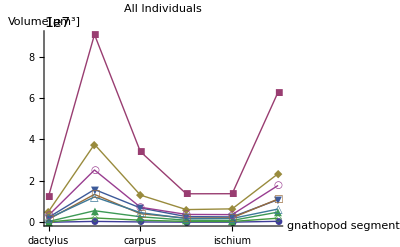

```mathematica
Needs["PlotLegends`"];
j=0;
myTickList=List[Map[List[j+=1,#]&,mySegmentsList],Automatic];

ListPlot[Transpose[myGraphList],PlotMarkers->Automatic,PlotLabel->"All Individuals",PlotLegend->myTempBaseNameList,LegendPosition->{0.7,-0.4},LegendSize->{.8,.5},LegendShadow->{0.01,-0.01},PlotRange->All,PlotRangePadding->1,Joined->True,AxesLabel->{"gnathopod segment","Volume[µm^3]"},Ticks->myTickList]

Clear[j]
```

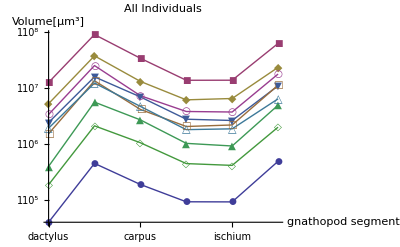

```mathematica
Options[ListLogPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}